# Meissner effect for rotating black holes

The Meissner effect for rotating black holes describes the expulsion of stationary axisymmetric magnetic fields from the outer horizon when the black hole reaches its maximum angular momentum.

## History and references

The Meissner effect, originally discovered by Meissner and Ochsenfeld in 1933, describes the expulsion of magnetic fields from a superconductor when it is cooled below a critical temperature T_c, marking the transition to the superconducting state.

Pictorial representation of the Meissner effect for superconductors. [Wikipedia]

In this topic exploration, we would like to explain the Meissner-like effect for rotating black holes. 
In the picture below, the circumference depicts the event horizon of the black hole and the spacetime outside the horizon is permeated by the electromagnetic field which does not deform the geometry of the spacetime (i.e., the electromagnetic field is a test field). The plot on the left shows that the field lines of the magnetic field penetrate the event horizon, while the plot on the right shows that the magnetic field lines are expelled out from the event horizon for a black hole rotating with its maximum angular momentum: this is the Meissner-like effect for rotating black holes.

Meissner-like effect for rotating black holes.
[Bičák, J., Karas, V., & Ledvinka, T. (2006). Black holes and magnetic fields. Proceedings of the International Astronomical Union, 2(S238), 139-144.]

The story of the Meissner-like effect starts with an elegant paper by R. Wald in 1974 [Phys. Rev. D, 10, 1680]. By using a theorem of Papapetrou [Ann. Inst. Henri Poincare, Sect. A 4, 83], i.e., that a Killing vector in a vacuum spacetime generates a vacuum (i.e. source-free) solution to Maxwell’s equations in that spacetime, Wald constructed a stationary, axisymmetric solution to vacuum Maxwell’s equations around Kerr spacetime. 
One year later, in 1975, King, Lasota and Kundt [Phys. Rev. D, 12, 3037] computed the flux of the magnetic field across the upper hemisphere of the event horizon as a function of the angular momentum of the Kerr black hole. They concluded that the magnetic flux is vanishing for maximally rotating black holes, establishing the Meissner-like effect for rotating black holes. Ten years later, Bičàk and Janiš [Mon Not R Astron Soc (1985) 212 (4): 899-915] confirmed this effect for back-reacting Maxwell’s fields, by explicitly solving the vacuum Maxwell’s equations around Kerr spacetime.

## Geometric background: the Kerr spacetime

Convention:
1. Newton constant G = 1, speed of light c = 1 (geometrized units); 
2. Indices of covariant tensors are denoted by lower-case letters, e.g., Tdddd stands for T_αβγδ, while indices of contravariant tensors are denoted by upper-case letters, e.g. TUUUU stands for T^αβγδ;
3. Tensor contraction is written as TUUU . TddU and it means T^αβγT_γδ^σ

A rotating black hole is described by the Kerr spacetime. 
In order to have a physical intuition of it, let us consider a sphere rotating around an axis:

```mathematica
Graphics3D[{{Green,Opacity[.35],Sphere[{0,0,0},1]},Text["rotation axis",{3,1.3,0}],
{Blue,Arrow[{{0,0,-1.5},{0,0,2}}],Line[Append[0]/@Append[#,First@#]&[CirclePoints[1,100]]]}},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

It exhibits an axial symmetry, because it looks the same if it is rotated by any angle around the rotation axis and it is constant in time.

The Kerr black hole is a stationary (constant in time) and axial-symmetric (it exhibits rotational symmetry around its axis of rotation) solution to the vacuum Einstein’s field equations.
It is parametrized by its mass m and its angular momentum J or, equivalently, by its angular momentum per unit mass a = J/m.

We define the coordinates to describe our spacetime in four dimensions:

```mathematica
coordinates={t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
dimension=Length[coordinates]
```

4

The spacetime is described by a symmetric metric tensor as follows:

```mathematica
gdd={{gtt[r, θ],0,0,gtϕ[r,θ]},{0,grr[r,θ],0,0},{0,0,gθθ[r,θ],0},{gtϕ[r,θ],0,0,gϕϕ[r,θ]}};
gdd//MatrixForm
```

(gtt[r,θ] | 0 | 0 | gtϕ[r,θ]
0 | grr[r,θ] | 0 | 0
0 | 0 | gθθ[r,θ] | 0
gtϕ[r,θ] | 0 | 0 | gϕϕ[r,θ])

where

```mathematica
gtt[r_,θ_]:=-((Σ[r,θ]Δ[r,θ])/A[r,θ])+A[r,θ]/Σ[r,θ] ΩZ^2 Sin[θ]^2
```

```mathematica
gtϕ[r_,θ_]:=-A[r,θ]/Σ[r,θ]ΩZ Sin[θ]^2
```

```mathematica
gϕϕ[r_,θ_]:=A[r,θ]/Σ[r,θ] Sin[θ]^2
```

```mathematica
grr[r_,θ_]:=Σ[r,θ]/Δ[r,θ]
```

```mathematica
gθθ[r_,θ_]:=Σ[r,θ]
```

and

```mathematica
Σ[r_,θ_]:=r^2+a^2Cos[θ]^2
```

```mathematica
Δ[r_,θ_]:=r^2-2m r +a^2
```

```mathematica
A[r_,θ_]:=(r^2+a^2)^2-a^2Δ[r,θ]Sin[θ]^2
```

```mathematica
ΩZ=(2m a r)/A[r,θ];
```

We notice that the function grr(r, θ) blows up at a specific radial location. Let us set m = 1, a = 0.3 m, and we look at the profile of g_rr(r, θ =π/2).

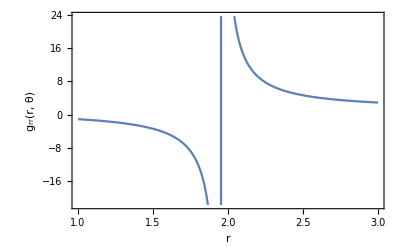

```mathematica
Plot[grr[r,π/2]/.m->1/.a->0.3,{r,1,3}, Frame->True, FrameLabel->{"r","g_rr(r, θ)"}]
```

Obviously, the location where the function g_rr blows up depends on the mass parameter m and tha angular momentum per unit mass a.
Such a radius, where our coordinates description breaks down, is the radial location of the event horizon. Therefore, we solve Δ(r, θ) = 0 and we get:

```mathematica
Solve[Δ[r,θ]==0,r][[2]]
```

{r→m+√(-a^2+m^2)}

Hence, let r_h be the event horizon location:

```mathematica
Subscript[r, h]=m+√(-a^2+m^2);
```

It is a two dimensional sphere with radius r_h:

```mathematica
Graphics3D[{{Green,Opacity[.35],Sphere[{0,0,0},1]},{Blue,Arrow[{{0,0,0},{1,0,0}}],Text[Subscript["r","h"],{.65,0,0}],Line[Append[0]/@Append[#,First@#]&[CirclePoints[1,100]]]}},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

## Papapetrou-Wald construction of test electromagnetic fields

#### Killing vectors: definition

As claimed before, the Kerr black hole is a stationary and axial-symmetric spacetime. To express the concept of stationarity and axial-symmetric in a precise mathematical way, we need to introduce the Killing vectors.

A vector field ξ is said Killing vector for the metric tensor g_μν if it preserves the metric, i.e., if the Lie derivative of the metric g_μν with respect the vector ξ is zero. In formulae, 
0 = ℒ_ξ g_μν = ξ^α∂_α g_μν+ g_αν∂_μ ξ^α +g_μα∂_ν ξ^α = ξ_(μ;ν) + ξ_(ν;μ), where the semicolon stands for covariant derivative operation (see below for its definition).

Let us define the Lie derivative operation from the second equality in the expression above:

```mathematica
Liedd[metric_List,coord_List,xiU_List] :=
Module[{tmp,ρ,μ,ν,dim},dim = Length[coord];  
Table[tmp= 0;
Do[
tmp =tmp + D[metric[[μ,ν]],coord[[ρ]]]xiU[[ρ]]+D[xiU[[ρ]],coord[[μ]]] metric[[ρ,ν]]+D[xiU[[ρ]],coord[[ν]]] metric[[μ,ρ]],
{ρ,dim}
]; 
tmp,{μ,dim},{ν,dim}]]
```

#### Killing vectors of Kerr Spacetime

Kerr spacetime is a stationary and axisymmetric spacetime. This implies that it has two commuting Killing vectors:

1. the timelike Killing vector η = η^μ∂_μ:

```mathematica
ηU = {1,0,0,0}
```

{1,0,0,0}

Its contravariant expression is η_μ = g_μν η^ν:

```mathematica
ηd = Simplify[gdd . ηU]
```

{-(a^2+2 r (-2 m+r)+a^2 Cos[2 θ])/(a^2+2 r^2+a^2 Cos[2 θ]),0,0,-(2 a m r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)}

Its norm is η^2 = η_μ η^μ. Asymptotically (for r -> ∞) it equals -1, from which we give the name timelike Killing vector:

```mathematica
Simplify[Normal[Series[ηU . ηd,{r,∞,0}]]]
```

-1

2. the axial Killing vector ψ = ψ^μ∂_μ:

```mathematica
ψU = {0,0,0,1}
```

{0,0,0,1}

with contravariant expression given by ψ_μ = g_μν ψ^ν:

```mathematica
ψd = Simplify[gdd . ψU]
```

{-(2 a m r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2),0,0,(Sin[θ]^2 ((a^2+r^2)^2-a^2 (a^2+r (-2 m+r)) Sin[θ]^2))/(r^2+a^2 Cos[θ]^2)}

It is easy to check that both η and ψ are two Killing vectors:

```mathematica
Liedd[gdd,coordinates,ηU]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Liedd[gdd,coordinates,ψU]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

#### Construction of electromagnetic fields

Following the Papapetrou-Wald construction, we now construct the test (i.e. not deforming the geometry) electromagnetic fields generated by the timelike and axial Killing vectors.
In this geometric construction, the Killing vectors serve as gauge potentials. Therefore, the associated electromagnetic field tensors are (F^(ξ))_μν =   ξ_(ν;μ) - ξ_(μ;ν) =  - 2 ξ_(μ;ν), where in the second step we have used the property of Killing vectors.

In order to proceed we need to define the covariant derivative operation. 
For a vector field, the covariant derivative reads as ξ_(μ;ν) = ∂_ν ξ_μ - (Γ^γ)_μν ξ_γ, where (Γ^γ)_μν = 1/2 g^γκ(∂_μ g_κν + ∂_ν g_μκ - ∂_κ g_μν) are the Christoffel symbols of the second kind.

Here, we define the Christoffel symbols:

```mathematica
gUU= Simplify[Inverse[gdd]];
```

```mathematica
ΓUdd =Simplify[ (1/2)Table[Sum[gUU[[γ,κ]]*(D[gdd[[κ,ν]],coordinates[[μ]]]+D[gdd[[μ,κ]],coordinates[[ν]]]-D[gdd[[μ,ν]],coordinates[[κ]]]),{κ,1,dimension}],{γ,1,dimension},{μ,1,dimension},{ν,1,dimension}]];
```

For example, the (Γ^t)_(r ϕ) component is given by

```mathematica
ΓUdd[[1,2,4]]
```

(a m (a^4-3 a^2 r^2-6 r^4+a^2 (a^2-r^2) Cos[2 θ]) Sin[θ]^2)/(2 (a^2+r (-2 m+r)) (r^2+a^2 Cos[θ]^2)^2)

We are now in the position to compute the covariant derivative of η and ψ and therefore the associated electromagnetic field tensor F^(η)and F^(ψ):

```mathematica
Fηdd=Simplify[-2Table[D[ηd[[μ]],coordinates[[ν]]] - Sum[ΓUdd[[γ,μ,ν]]*ηd[[γ]],{γ,1,dimension}],{μ,1,dimension},{ν,1, dimension}]];
```

```mathematica
Fψdd=Simplify[-2Table[D[ψd[[μ]],coordinates[[ν]]] - Sum[ΓUdd[[γ,μ,ν]]*ψd[[γ]],{γ,1,dimension}],{μ,1,dimension},{ν,1, dimension}]];
```

and we construct the following linear combination

```mathematica
Fdd = Simplify[(1/2)B0(Fψdd+2a Fηdd)-(Q/(2m)Fηdd)];
```

Here, B0 is the asymptotic value (at r -> ∞) of the magnetic field strength and Q is the charge of the black hole. In the following, we simply set Q = 0.

We might check that this electromagnetic field tensor comes from the vector potential

```mathematica
Ad=Simplify[(1/2)B0(ψd+2a ηd)-(Q/(2m)ηd)]
```

{(-2 a^3 B0 m+a^2 Q+2 a B0 m (3 m-2 r) r+2 Q r (-2 m+r)+a (-2 a^2 B0 m+a Q+2 B0 m^2 r) Cos[2 θ])/(2 m (a^2+2 r^2+a^2 Cos[2 θ])),0,0,(Sin[θ]^2 (a^4 B0+2 a Q r+B0 r^4+2 a^2 B0 r (-2 m+r)-a^2 B0 (a^2+r (-2 m+r)) Sin[θ]^2))/(2 (r^2+a^2 Cos[θ]^2))}

```mathematica
Fdd==Simplify[-2Table[D[Ad[[μ]],coordinates[[ν]]] - Sum[ΓUdd[[γ,μ,ν]]*Ad[[γ]],{γ,1,dimension}],{μ,1,dimension},{ν,1, dimension}]]//Simplify
```

True

In the next section, we aim at computing the magnetic flux though the event horizon.

## Computation of the magnetic flux

We want to compute the flux of the magnetic field across the upper hemisphere of the event horizon.
We define the magnetic flux as the integral of the electromagnetic tensor (which is a two-form) over a two-dimensional surface:
Φ_B = (1/2π)∫_(H^+) F  =  (1/2π)∫_(H^+) dA =  (1/2π)∫_(∂H^+) A
where we have written F = dA in the second step and we have used the Stokes’ theorem in the third step. 
∂H^+ stands for the boundary of the upper hemisphere H^+ of the event horizon surface. It is a circumference of radius r = r_horizon on the equatorial plane θ = π/2.

Here is a visualization of it: ∂H^+ is highlighted in red.

```mathematica
Graphics3D[{FaceForm[Green,Blue],Opacity[0.5],Sphere[], {Red,Thickness[0.02],Line[Append[0]/@Append[CirclePoints[1,100],First[CirclePoints[1,100]]]]},Text[Style["H^+",20],{0,0,1.3}],Text[Style["TraditionalForm`∂H^+",20],{0,-1.2,0}]},ClipPlanes->{{0,0,1,0}},ClipPlanesStyle->{Directive[Opacity[.6],Blue]}, Boxed->False]
```

-Graphics3D-

Therefore, the magnetic flux is simply given by Φ_B =  (1/2π)∫_(∂H^+) A =  (1/2π)(∫_0)^(2π)A_ϕ dϕ = A_ϕ(r = r_horizon, θ=π/2), because A_ϕ is independent of ϕ.

```mathematica
Flux = Simplify[Ad[[4]]/.{r->Subscript[r, h], θ->π/2}]
```

(-2 a^2 B0 m+2 B0 m^2 (m+√(-a^2+m^2))+a Q)/(m+√(-a^2+m^2))

which can be rewritten in a more readable way as

```mathematica
Flux==(1/2)B0 Subscript[r, h]^2(1+a^2/Subscript[r, h]^2)(1-(a/Subscript[r, h])^2(1-Q/(a m B0)))//Simplify
```

True

The magnetic flux is a function of a (the angular momentum per unit mass), m (mass), the asymptotic value of the magnetic field B0 and the charge of the black hole Q.
We set the mass parameter m = 1, the charge Q = 0 and the asymptotic value of the magnetic field B0 = 1 and study the flux as a function of a in the range [0, 1], where we have a real radial location for r_h.

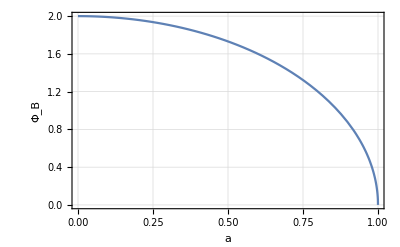

```mathematica
Plot[Flux/.{Q->0, m->1, B0->1},{a,0,1}, FrameLabel->{"a","Φ_B"}, PlotTheme->"FrameGrid"]
```

and we plot the near-extremal range [0.9, 1]:

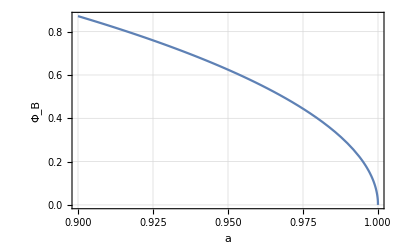

```mathematica
Plot[Flux/.{Q->0, m->1, B0->1},{a,0.9,1}, FrameLabel->{"a","Φ_B"}, PlotTheme->"FrameGrid"]
```

As it is clear from the last two plots, when the black hole rotates with its maximal angular momentum, a = m = 1, the magnetic flux is zero:

```mathematica
Flux/.{Q->0, m->1, B0->1}/.a->1
```

0

This is the Meissner-like effect for rotating black holes! Notice that this effect is not present if the black hole is charged Q ≠ 0.

## Visualization of the Meissner-like effect

We set

```mathematica
Q=0;
B0=1;
m=1;
```

Now, we would like to visualize the Meissner-like effect in the (r, θ)-plane. 
Here, we plot the contour lines of constant magnetic flux. The vertical red line is the radial location of the event horizon r_h= m + √m^2-a^2.

For a < 1, the magnetic flux penetrates the event horizon:

```mathematica
ContourPlot[{Ad[[4]]}/.a->0.9,{r,0.9,10},{θ,0,π}, FrameLabel->{"r", "Φ_B"},GridLines->{{{1+Sqrt[1-a^2]/.a->0.9,{Thick,Red}}}, None},Contours->100, PlotPoints->80, PlotLegends->Automatic,PerformanceGoal->"Speed"]
```

-Graphics-

For a = 1, the magnetic flux is expelled out, according to our analysis in the previous section:

```mathematica
ContourPlot[{Ad[[4]]}/.a->1,{r,0.9,10},{θ,0,π}, FrameLabel->{"r", "Φ_B"},GridLines->{{{1+Sqrt[1-a^2]/.a->1,{Thick,Red}}}, None},Contours->100, PlotPoints->80, PlotLegends->Automatic,PerformanceGoal->"Speed"]
```

-Graphics-

We explore the whole range of the angular momentum and do an animation to highlight the Meissner-like effect:

```mathematica
plots=Table[ContourPlot[Ad[[4]]/.a->c,{r,1,10},{θ,0,π},GridLines->{{{1+Sqrt[1-a^2]/.a->c,{Thick,Red}}}, None},Contours->200,  PlotLegends->Automatic,PerformanceGoal->"Speed"],{c,0,1,0.05}];
```

```mathematica
ListAnimate[plots]
```

Further Explorations

Study the orbit a test particle around Kerr spacetime

Study of the gravitational radiation emitted by a particle spiralling around Kerr spacetime

Authorship information

Roberto Oliveri

Friday, June 23rd 2017

roliveri@ulb.ac.be